## Available energy NAE

### Second adiabatic invariant

The main idea is to calculate
,

the second adiabatic invariant in a perturbative form using a near-axis model for the magnetic field magnitude. To do that, and using Boozer coordinates and the usual NAE notation (using a mixed notation between [Landreman, 2019] and [Rodriguez, 2020]), we write,

,

where χ = θ-Nϕ is the direction of the symmetry of the magnetic field, which we have normalised to B_0.

#### Definitions and nae:

λ:

The trapped particle pitch label λ is defined in terms of the first adiabatic invariant and the energy H as,

,

which will become important when taking partial derivatives later.

Magnetic field magnitude:

We separate the magnetic field into two pieces,

```mathematica
Bbar=1-r η Cos[χ];
```

And,

```mathematica
deltaB=r^2(B20+B2c Cos[2χ]);
```

where the parameters all have their usual meaning within the near-axis expansion. In particular, , assuming for simplicity that ψ>0. Note also that we have defined η with a minus sign in comparison to the usual convention so that the bounce integrals involved in  may be taken most easily about χ=0 as the minimum of the magnetic well. We are of course assuming stellarator symmetry and exact QS behaviour.

Other nae quantities:

We also expand the Jacobian and current related  and the rotational transform .

```mathematica
Ba=Ba0+r^2 Ba1;
iotaN=iotaN0+r^2 iota1;
```

Bounce points:

With this, we may define the bounce points as the values of χ_b at which 
.

#### Expansion 1st order

We are interested in expanding the expression,

```mathematica
JparFac=Sqrt[2 H] Ba/(iotaN B0);
JparInt=Sqrt[1-λ((Bb[χ]+dBb)+ϵ(dB[χ]-dBb))]/(Bb[χ]+ϵ dB[χ]);
```

Expansion in ϵ:

Let us consider an expansion in ϵ of the integral above (not including the integral sign for simplicity),

```mathematica
Jpar0int= FullSimplify[SeriesCoefficient[JparInt,{ϵ,0,0}]]
```

(√(1-dBb λ-λ Bb[χ]))/Bb[χ]

and to the next order,

```mathematica
Jpar1int= FullSimplify[SeriesCoefficient[JparInt,{ϵ,0,1}]]
```

(2 (-1+dBb λ) dB[χ]+λ Bb[χ] (dBb+dB[χ]))/(2 Bb[χ]^2 √(1-dBb λ-λ Bb[χ]))

where the multiplicative factor has been left out for now.

1st order:

Let us then focus on the leading order, and introduce,

```mathematica
Jpar0int=FullSimplify[Jpar0int/.{Bb[χ]->Bbar}]
```

-(√(1-(1+dBb) λ+r η λ Cos[χ]))/(-1+r η Cos[χ])

Let us then introduce the following definition of k^2,

```mathematica
lamTok2={λ->1/(1+r η (2k2-1)+dBb)};
```

With which it follows simply that,

```mathematica
Jpar0int=Sqrt[λ]FullSimplify[Jpar0int/Sqrt[λ]/.lamTok2,Assumptions->{Element[_,Reals],1+dBb+(-1+2 k2) r η>0}]
```

(√λ √(r η (-1+2 k2+Cos[χ])))/(1-r η Cos[χ])

which is precisely the term in (A2).

With this expression at hands, let us now define a , and k sin ζ=sin X,

```mathematica
XtoZeta={Sin[X]->k Sin[ζ],Cos[X]->Sqrt[1-k2 Sin[ζ]^2]};
```

```mathematica
Jpar0int=FullSimplify[FullSimplify[TrigExpand[Jpar0int/.χ->2X]/.{Cos[2 X]->1-2 Sin[X]^2}/.XtoZeta/.k^2 ->k2/.{Cos[2 ζ]->1-2 Sin[ζ]^2},Assumptions->0<ζ<Pi/2]/.{1+Cos[2 ζ]->2 Cos[ζ]^2},Assumptions->0<ζ<Pi/2]
```

(√2 √(k2 r η) √λ Cos[ζ])/(1+(-1+k2) r η-k2 r η Cos[2 ζ])

Because we are inside an integral, we must not forget to transform χ to X to ζ,

```mathematica
dchidX=2;
dXdzeta=(k Cos[ζ])/Sqrt[1-k2 Sin[ζ]^2];
dchidzeta=dchidX dXdzeta
```

(2 k Cos[ζ])/(√(1-k2 Sin[ζ]^2))

Thus, the integral

```mathematica
Jpar0intF=Simplify[FullSimplify[Jpar0int dchidzeta]/.{Cos[2 ζ]->1-2 Sin[ζ]^2}]
```

(2 √2 k √(k2 r η) √λ Cos[ζ]^2)/(√(1-k2 Sin[ζ]^2) (1-r η+2 k2 r η Sin[ζ]^2))

Together with the appropriate factors now, and expanding now in powers of r,

```mathematica
Jpar0a=SeriesCoefficient[Jpar0intF JparFac,{r,0,1/2}]
```

(4 Ba0 √H k √(k2 η) √λ Cos[ζ]^2)/(B0 iotaN0 √(1-k2 Sin[ζ]^2))

```mathematica
Jpar0b=FullSimplify[SeriesCoefficient[Jpar0intF JparFac,{r,0,3/2}]]
```

(4 Ba0 √H k √(k2 η) √λ Cos[ζ]^2 (η-2 k2 η Sin[ζ]^2))/(B0 iotaN0 √(1-k2 Sin[ζ]^2))

Noting that one would have to go to the next order to get the pressure and the magnetic shear explicitly involved in these expressions.

```mathematica
Jpar0c=FullSimplify[SeriesCoefficient[Jpar0intF JparFac,{r,0,5/2}]]
```

(4 √H k √(k2 η) √λ Cos[ζ]^2 (-Ba0 iota1+Ba1 iotaN0+Ba0 iotaN0 η^2+4 Ba0 iotaN0 k2 η^2 Sin[ζ]^2 (-1+k2 Sin[ζ]^2)))/(B0 iotaN0^2 √(1-k2 Sin[ζ]^2))

We shall not deal with this order further (noting that one should in this case pose questions about he interpretation of the nae model, and its truncation thereof, especially when considering the Jacobian for the integral measure).

Jpar0a:

Let us now compute the integral by taking,

```mathematica
Jpar0aTot=Simplify[Limit[Integrate[Jpar0a,{ζ,-a,a},GenerateConditions->False],a->Pi/2]/.k2->k^2,Assumptions->k>0]
```

(8 Ba0 √H √η √λ (EllipticE[k^2]+(-1+k^2) EllipticK[k^2]))/(B0 iotaN0)

So that we may define the function 
.

Thus,

```mathematica
I1fun=2(EllipticE[k^2]+(-1+k^2) EllipticK[k^2]);
Jpar0aTot=(4 Ba0 √(H η λ))/(B0 iotaN0)I1[k];
```

Jpar0b:

Let us now compute the integral by taking,

```mathematica
Jpar0bTot=Simplify[Limit[Integrate[Jpar0b,{ζ,-a,a},GenerateConditions->False],a->Pi/2]/.k2->k^2,Assumptions->k>0]
```

(8 Ba0 √H η^(3/2) √λ ((-1+2 k^2) EllipticE[k^2]-(-1+k^2) EllipticK[k^2]))/(3 B0 iotaN0)

So that we may define the function 
.

Thus,

```mathematica
I2fun=2/3((-1+2 k^2) EllipticE[k^2]-(-1+k^2) EllipticK[k^2]);
Jpar0bTot=(4 Ba0 η √(H η λ))/(B0 iotaN0)I2[k];
```

Consistent 1st order:

Taking into account the expansion for λ, we end up having,

```mathematica
Jpar0tot=FullSimplify[Series[(r^(1/2)Jpar0aTot+r^(3/2)Jpar0bTot)/.lamTok2/.{k2->k^2}/.dBb->r^2 dBb,{r,0,2}]]
```

(4 Ba0 √(H η) I1[k] √r)/(B0 iotaN0)+(2 Ba0 η √(H η) (I1[k]-2 k^2 I1[k]+2 I2[k]) r^(3/2))/(B0 iotaN0)+O[r]^(5/2)

Which reads as in the paper,

#### Expansion 2nd order

2nd order:

Let us then focus on the leading order, and introduce,

```mathematica
Jpar1int= FullSimplify[SeriesCoefficient[JparInt,{ϵ,0,1}]]
```

(2 (-1+dBb λ) dB[χ]+λ Bb[χ] (dBb+dB[χ]))/(2 Bb[χ]^2 √(1-dBb λ-λ Bb[χ]))

```mathematica
Jpar1int=FullSimplify[Jpar1int/.{Bb[χ]->Bbar}]
```

(2 (-1+dBb λ) dB[χ]+λ (1-r η Cos[χ]) (dBb+dB[χ]))/(2 (-1+r η Cos[χ])^2 √(1-(1+dBb) λ+r η λ Cos[χ]))

Let us then introduce the following definition of k^2,

```mathematica
lamTok2={λ->1/(1+r η (2k2-1)+dBb)};
```

and also use,

```mathematica
deltaBsub={dB[χ]->r^2 B2c (Cos[2χ]-Cos[2 Subscript[χ, b]])+dBb};
```

With which it follows simply that,

```mathematica
Jpar1int=FullSimplify[Jpar1int/.lamTok2/.deltaBsub,Assumptions->{Element[_,Reals],1+dBb+(-1+2 k2) r η>0}]
```

(r (-2 dBb η (-1+2 k2+Cos[χ])-B2c r (1+2 (-1+2 k2) r η+r η Cos[χ]) Cos[2 χ]+B2c r (1+2 (-1+2 k2) r η+r η Cos[χ]) Cos[2 χ_b]))/(2 √(r η (1+dBb+(-1+2 k2) r η) (-1+2 k2+Cos[χ])) (-1+r η Cos[χ])^2)

which we would like to expand in powers of r (thus including the factor in front of the integral), and the leading order being r^(3/2),

```mathematica
Jpar1a=SeriesCoefficient[Jpar1int JparFac/.{dBb->r^2},{r,0,3/2}]
```

(Ba0 √H (-B2c Cos[2 χ]+B2c Cos[2 χ_b]))/(√2 B0 iotaN0 √(η (-1+2 k2+Cos[χ])))

which as argued is the leading contributor to this part of the second adiabatic invariant.

With this expression at hands, let us now define as before a , and k sin ζ=sin X, and using the definition cos χ_b=1-2 k^2,

```mathematica
XtoZeta={Sin[X]->k Sin[ζ],Cos[X]->Sqrt[1-k2 Sin[ζ]^2]};
```

```mathematica
Jpar1aInt=FullSimplify[FullSimplify[FullSimplify[TrigExpand[Jpar1a/.{χ->2X,Subscript[χ, b]->2 Subscript[X, b]}]/.{Cos[2 X]->1-2 Sin[X]^2}/.XtoZeta/.k^2 ->k2/.{Cos[2 ζ]->1-2 Sin[ζ]^2},Assumptions->0<ζ<Pi/2]/.{1+Cos[2 ζ]->2 Cos[ζ]^2},Assumptions->0<ζ<Pi/2]/.Sin[2 Subscript[X, b]]->Sqrt[1-(1-2k2)^2]]
```

-(B2c Ba0 √H Sec[ζ] (-8 (-1+k2) k2-8 k2 Sin[ζ]^2+(k^4+7 k2^2) Sin[ζ]^4))/(2 B0 iotaN0 √(k2 η))

Because we are inside an integral, we must not forget to transform χ to X to ζ,

```mathematica
dchidX=2;
dXdzeta=(k Cos[ζ])/Sqrt[1-k2 Sin[ζ]^2];
dchidzeta=dchidX dXdzeta
```

(2 k Cos[ζ])/(√(1-k2 Sin[ζ]^2))

Thus, the integral

```mathematica
Jpar1intF=Simplify[FullSimplify[Jpar1aInt dchidzeta/.{k2->k^2},Assumptions->k>0]/.{Cos[2 ζ]->1-2 Sin[ζ]^2}]
```

(8 B2c Ba0 √H k^2 Cos[ζ]^2 (-1+k^2+k^2 Sin[ζ]^2))/(B0 iotaN0 √η √(1-k^2 Sin[ζ]^2))

Performing the integral:

Let us now compute the integral expicitly,

```mathematica
Jpar1Tot=Simplify[Limit[Integrate[Jpar1intF,{ζ,-a,a},GenerateConditions->False],a->Pi/2]/.k2->k^2,Assumptions->k>0]
```

(16 B2c Ba0 √H ((-1+2 k^2) EllipticE[k^2]+(1-4 k^2+3 k^4) EllipticK[k^2]))/(3 B0 iotaN0 √η)

Which we may write in terms of a function I_22^c,

.

To show that this is the case, it suffices to use,

```mathematica
Simplify[4/3((-1+2 k^2) EllipticE[k^2]+(1-4 k^2+3 k^4) EllipticK[k^2])+(I2fun-(2 k^2-1)I1fun)]
```

0

Thus,

```mathematica
I22cfun=I2fun-(2 k^2-1)I1fun;
Jpar1Tot=-4 √(H η r)Ba0/(B0 iotaN0) r/η B2c I22c[k];
```

Total  to second order in the expansion:

```mathematica
JparTot=Jpar0tot+Jpar1Tot
```

(4 Ba0 √(H η) I1[k] √r)/(B0 iotaN0)+((2 Ba0 η √(H η) (I1[k]-2 k^2 I1[k]+2 I2[k]))/(B0 iotaN0)-(4 B2c Ba0 √(H η) I22c[k])/(B0 iotaN0 η)) r^(3/2)+O[r]^(5/2)

which is precisely Eq. (2.24) in the paper.

### Precession ω_α

Once we have computed the second adiabatic invariant we are in a position to compute ω_α by taking the appropriate partial derivatives of .

#### Important definitions

To compute the partial derivatives of , we need to bear in mind respect to which variables we are taking such derivatives: H, μ, ψ.

k^2:

Let us start with the definition of , so that the bounce  is,

```mathematica
bounceTok={Cos[Subscript[χ, b]]->1-2 k^2,Sin[Subscript[χ, b]]->Sqrt[1-(1-2 k^2)^2]};
dBbinK=FullSimplify[TrigExpand[deltaB/.{χ->Subscript[χ, b]}]/.bounceTok]
```

(B20+B2c-8 B2c k^2+8 B2c k^4) r^2

Then, from the definition of k^2,

```mathematica
eqK=1/λ-(1+r η (2 k^2-1)+dBb)==0/.{dBb->dBbinK};
```

λ:

We must note, though, that λ is not one of the explicit variables used neither, as it is defined to be

.

Thus, we define,

```mathematica
dlamdH=-λ/H;
```

r:

The pseudo-radial variable r is defined to be

.

Thus,

```mathematica
drdpsi=1/(r B0);
```

#### Partial derivatives

Δα:

We need,

.

:

Let us start by computing this partial derivative. To that end, take

```mathematica
dkdr=k'[r]/.Solve[D[eqK/.k->k[r],r],k'[r]][[1]][[1]]/.{k[r]->k}
```

(-2 B20 r-2 B2c r+16 B2c k^2 r-16 B2c k^4 r+η-2 k^2 η)/(4 k r (-4 B2c r+8 B2c k^2 r+η))

where it is important to note that λ has no r dependence. Expanded,

```mathematica
Series[dkdr,{r,0,0}]
```

(1-2 k^2)/(4 k r)+(-B20+B2c)/(2 k η)+O[r]^1

which is (C1d).

:

We will need the derivatives of the functions I_1, I_2 and I_22^c with respect to k to compute the partial derivatives appropriately. So

```mathematica
dI1dk=Simplify[D[I1fun,k]]
```

2 k EllipticK[k^2]

```mathematica
dI2dk=Simplify[D[I2fun,k]]
```

4 k EllipticE[k^2]-2 k EllipticK[k^2]

```mathematica
dI22cdk=Simplify[D[I22cfun,k]]
```

-4 k (EllipticE[k^2]+(-2+3 k^2) EllipticK[k^2])

With this, we now compute,

```mathematica
IfunSub={I1'[k]->dI1dk,I2'[k]->dI2dk,I22c'[k]->dI22cdk,I1[k]->I1fun,I2[k]->I2fun,I22c[k]->I22cfun};
```

```mathematica
dJpardk=FullSimplify[D[JparTot,k]/.IfunSub]
```

(8 Ba0 k √(H η) EllipticK[k^2] √r)/(B0 iotaN0)+(4 Ba0 H k (4 B2c EllipticE[k^2]+(4 B2c (-2+3 k^2)+3 (1-2 k^2) η^2) EllipticK[k^2]) r^(3/2))/(B0 iotaN0 √(H η))+O[r]^(5/2)

With this partial derivative, we may thus compute,

```mathematica
JparTot
```

(4 Ba0 √(H η) I1[k] √r)/(B0 iotaN0)+((2 Ba0 η √(H η) (I1[k]-2 k^2 I1[k]+2 I2[k]))/(B0 iotaN0)-(4 B2c Ba0 √(H η) I22c[k])/(B0 iotaN0 η)) r^(3/2)+O[r]^(5/2)

```mathematica
dJpardpsi=FullSimplify[Series[D[JparTot,r]drdpsi+dJpardk dkdr drdpsi,{r,0,2}]/.IfunSub]
```

-(2 (Ba0 √(H η) (-2 EllipticE[k^2]+EllipticK[k^2])))/((B0^2 iotaN0) r^(3/2))+(Ba0 H (2 (-1+2 k^2) (2 B2c-η^2) EllipticE[k^2]+(-4 B20+4 B2c-4 B2c k^2+η^2+2 k^2 η^2) EllipticK[k^2]))/(B0^2 iotaN0 √(H η) √r)+√O[r]

Which by order,

```mathematica
dJpardpsi0=FullSimplify[SeriesCoefficient[D[JparTot,r]drdpsi+dJpardk dkdr drdpsi,{r,0,-3/2}]/.IfunSub]
```

-(2 Ba0 √(H η) (-2 EllipticE[k^2]+EllipticK[k^2]))/(B0^2 iotaN0)

And the next order correction (factoring B0^2 iota/Ba0 (Hη)^(1/2) out),

```mathematica
dJpardpsi1=Collect[FullSimplify[SeriesCoefficient[D[JparTot,r]drdpsi+dJpardk dkdr drdpsi,{r,0,-1/2}]/.IfunSub,Assumptions->H>0],{B20,B2c}]
```

-(4 B20 Ba0 H EllipticK[k^2])/(B0^2 iotaN0 √(H η))+(B2c Ba0 H (4 (-1+2 k^2) EllipticE[k^2]+4 EllipticK[k^2]-4 k^2 EllipticK[k^2]))/(B0^2 iotaN0 √(H η))+(Ba0 H (-2 (-1+2 k^2) η^2 EllipticE[k^2]+η^2 EllipticK[k^2]+2 k^2 η^2 EllipticK[k^2]))/(B0^2 iotaN0 √(H η))

```mathematica
dJpardpsi1fac=Collect[Simplify[(B0^2 iotaN0)/(Ba0 √(H η))dJpardpsi1],{B20,B2c}]
```

-(4 B20 EllipticK[k^2])/η+(B2c (4 (-1+2 k^2) EllipticE[k^2]+4 EllipticK[k^2]-4 k^2 EllipticK[k^2]))/η+(-2 (-1+2 k^2) η^2 EllipticE[k^2]+η^2 EllipticK[k^2]+2 k^2 η^2 EllipticK[k^2])/η

Which is precisely the expression in (C2).

τ_b:

For the bounce time, we simply need to compute the derivatives with respect to H.

:

For this we need,

```mathematica
dkdlambda=Simplify[k'[λ]/.Solve[D[eqK/.k->k[λ],λ],k'[λ]][[1]][[1]]/.{k[λ]->k}/.lamTok2/.{k2->k^2}/.{dBb->dBbinK}]
```

-((1+(B20+B2c-8 B2c k^2+8 B2c k^4) r^2+(-1+2 k^2) r η)^2)/(4 k r (4 B2c (-1+2 k^2) r+η))

Thus,

```mathematica
dkdH=Simplify[dkdlambda dlamdH/.lamTok2/.{dBb->dBbinK}/.{k2->k^2}]
```

(1+(B20+B2c-8 B2c k^2+8 B2c k^4) r^2+(-1+2 k^2) r η)/(4 H k r (4 B2c (-1+2 k^2) r+η))

which expanded,

```mathematica
FullSimplify[Series[dkdH,{r,0,0}]]
```

1/(4 H k η r)+((-1+2 k^2) (-4 B2c+η^2))/(4 H k η^2)+O[r]^1

which is precisely (C1c) in the paper.

:

```mathematica
dJpardH=FullSimplify[Series[D[JparTot,H]+dJpardk dkdH ,{r,0,2}]/.IfunSub/.{k2->k^2}]
```

(2 Ba0 EllipticK[k^2])/(B0 iotaN0 √(H η) √r)+(Ba0 H (4 (B2c+η^2) EllipticE[k^2]+(-4 B2c k^2+(-3+2 k^2) η^2) EllipticK[k^2]) √r)/(B0 iotaN0 (H η)^(3/2))+O[r]^(3/2)

Which separated into its different orders,

```mathematica
dJpardH0=SeriesCoefficient[dJpardH,{r,0,-1/2}]
```

(2 Ba0 EllipticK[k^2])/(B0 iotaN0 √(H η))

```mathematica
dJpardH1=Collect[SeriesCoefficient[dJpardH,{r,0,1/2}],B2c]
```

(B2c Ba0 H (4 EllipticE[k^2]-4 k^2 EllipticK[k^2]))/(B0 iotaN0 (H η)^(3/2))+(Ba0 H (4 η^2 EllipticE[k^2]+(-3+2 k^2) η^2 EllipticK[k^2]))/(B0 iotaN0 (H η)^(3/2))

Which factored out,

```mathematica
dJpardH1fac=Collect[Simplify[(B0 iotaN0 √(H η))/Ba0 dJpardH1],B2c]
```

(B2c (4 EllipticE[k^2]-4 k^2 EllipticK[k^2]))/η+(4 η^2 EllipticE[k^2]+(-3+2 k^2) η^2 EllipticK[k^2])/η

which is (C3) in the paper.

#### ω_α evaluation

ω_α:

Thus,

```mathematica
walpha=Series[dJpardpsi/dJpardH,{r,0,1}]
```

-(H η (-2 EllipticE[k^2]+EllipticK[k^2]))/(B0 EllipticK[k^2] r)-1/(B0 EllipticK[k^2]^2)H (4 B2c EllipticE[k^2]^2+4 η^2 EllipticE[k^2]^2-8 B2c k^2 EllipticE[k^2] EllipticK[k^2]-6 η^2 EllipticE[k^2] EllipticK[k^2]+4 k^2 η^2 EllipticE[k^2] EllipticK[k^2]+2 B20 EllipticK[k^2]^2-2 B2c EllipticK[k^2]^2+4 B2c k^2 EllipticK[k^2]^2+η^2 EllipticK[k^2]^2-2 k^2 η^2 EllipticK[k^2]^2)+O[r]^1

Which separated in orders,

```mathematica
walpha0=SeriesCoefficient[walpha,{r,0,-1}]
```

-(H η (-2 EllipticE[k^2]+EllipticK[k^2]))/(B0 EllipticK[k^2])

Which we may write as,

```mathematica
Gfun=2 EllipticE[k^2]/EllipticK[k^2]-1;
walpha0=(H η)/(B0 r)G;
```

```mathematica
walpha1Or=Collect[FullSimplify[SeriesCoefficient[walpha,{r,0,0}]],{B2c,B20}]
```

-(2 B20 H)/B0-(B2c H (4 EllipticE[k^2]^2-8 k^2 EllipticE[k^2] EllipticK[k^2]+2 (-1+2 k^2) EllipticK[k^2]^2))/(B0 EllipticK[k^2]^2)-(H (4 η^2 EllipticE[k^2]^2-2 (3-2 k^2) η^2 EllipticE[k^2] EllipticK[k^2]-(-1+2 k^2) η^2 EllipticK[k^2]^2))/(B0 EllipticK[k^2]^2)

Which factored out,

```mathematica
walpha1fac=Collect[FullSimplify[B0/(H η)SeriesCoefficient[walpha,{r,0,0}]],{B2c,B20}]
```

-(2 B20)/η+(B2c (-4 EllipticE[k^2]^2+8 k^2 EllipticE[k^2] EllipticK[k^2]-2 (-1+2 k^2) EllipticK[k^2]^2))/(η EllipticK[k^2]^2)+(-4 η^2 EllipticE[k^2]^2+2 (3-2 k^2) η^2 EllipticE[k^2] EllipticK[k^2]+(-1+2 k^2) η^2 EllipticK[k^2]^2)/(η EllipticK[k^2]^2)

which is (C4) in the paper. We then define,

```mathematica
G20fun=-2;
G2cfun=-4((EllipticE[k^2]^2)/(EllipticK[k^2]^2)-2 k^2 EllipticE[k^2]/EllipticK[k^2]+( k^2-1/2));
G2fun=-4 (EllipticE[k^2]^2)/(EllipticK[k^2]^2)+2 (3-2 k^2)  EllipticE[k^2]/EllipticK[k^2] +(-1+2 k^2) ;
walpha1=(H η)/B0(B20/η G20+B2c/η G2c+η G2);
```

Just to check,

```mathematica
FullSimplify[(walpha1-walpha1Or)/.{G20->G20fun,G2c->G2cfun,G2->G2fun}]
```

0

ω_α (geometry):

Here we need the expressions for B_20 and B_(2c) in terms of the near-axis triangularity and pressure gradient. From mhd_express_matt_notation.nb, (noting that B20 in this document is really normalised to B_0, and thus taking that into account),

```mathematica
Clear[B20,B2c]
```

```mathematica
B20=-(1+(l^2 η^2)/Subscript[ι, 0]^2(4  Sqrt[α])/((α+3)-Fbar( α+1)))(mu0 p2)/B0^2-3/2((1-α)+Fbar(α+1))/(Fbar(α+1)-(3+α))η sη δ+Subscript[Λ, 0];
```

at an up-down symmetric cross-section, where Fbar has its usual meaning. For B2c,

```mathematica
B2c=-(2 mu0 p2)/B0^2(l^2 η^2)/Subscript[ι, 0]^2 Sqrt[α]/(Fbar(1+α)-(3+α))-1/2((3-α)+Fbar(1+α))/((3+α)-Fbar(1+α))η sη δ+Subscript[Λ, C];
```

Then,

```mathematica
walpha1dp=FullSimplify[Coefficient[Simplify[walpha1],{δ ,p2}]]
```

{(H sη (-3 G20 (1+Fbar+(-1+Fbar) α)+G2c (3+Fbar+(-1+Fbar) α)) η)/(2 B0 (-3+Fbar+(-1+Fbar) α)),(H mu0 (-G20+(2 (2 G20-G2c) l^2 √α η^2)/((-3+Fbar+(-1+Fbar) α) ι_0^2)))/B0^3}

To check the simplified expressions, with the assumption in the paper that η>0 (note that it only involves |η| from the factor in front of the triangularity)

```mathematica
walpha1dSimp=(H η)/(2 B0)((3(1-α)G20-(3-α)G2c)/((3+α)-(α+1)Fbar)+((α+1)(3G20-G2c)Fbar)/((3+α)-(α+1)Fbar));
```

```mathematica
Simplify[walpha1dp[[1]]-walpha1dSimp/.sη->1]
```

0

Similarly,

```mathematica
walpha1pSimp=-(H η)/B0 mu0/(η B0^2)(G20+((η l)/Subscript[ι, 0])^2(2Sqrt[α])/((3+α)-(α+1)Fbar)(2G20-G2c));
```

```mathematica
Simplify[walpha1dp[[2]]-walpha1pSimp]
```

0

ω_α Connor:

Let us now double check the comparison to Connor et al. For that, we need to first consider the definition of the pressure gradient parameter α_p,

,

a dimensionless measure of the pressure gradient. In terms of this, for a circle and axisymmetry,

```mathematica
Gptok=Collect[Simplify[B0/(H η)walpha1pSimp/.{Fbar->0,α->1,G20->G20fun,G2c->G2cfun,η->1}]/.mu0->-(ap η B0^2 Subscript[ι, 0]^2)/4/.{η->1,l->1},Subscript[ι, 0]]
```

(ap (2 EllipticE[k^2]^2-4 k^2 EllipticE[k^2] EllipticK[k^2]+(-3+2 k^2) EllipticK[k^2]^2))/(4 EllipticK[k^2]^2)-(ap ι_0^2)/2

```mathematica
GpConn=-(4 ap)/3 ((2 k^2-1) EllipticE[k^2]/EllipticK[k^2]+1-k^2 )-(ap Subscript[ι, 0]^2)/2;
```

Plotting them for comparison,

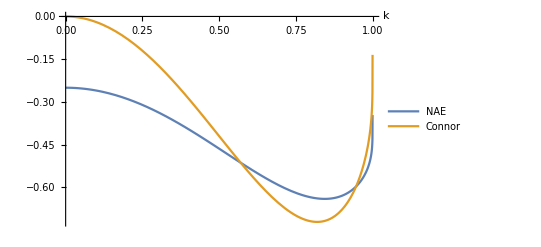

```mathematica
Plot[{Gptok/.{Subscript[ι, 0]->0,ap->1},GpConn/.{Subscript[ι, 0]->0,ap->1}},{k,0,1},PlotLegends->{"NAE","Connor"},AxesLabel->{k}]
```

which we want to compare to,

For the shear, consider

```mathematica
Clear[B20,B2c]
diotadpsi=(2 Subscript[ι, 1])/B0;
FullSimplify[r SeriesCoefficient[FullSimplify[(D[Jpar0tot,iotaN0]diotadpsi)/dJpardH/.{I1[k]->I1fun}],{r,0,1}]/.Subscript[ι, 1]->-iotaN0/(2 r^2)s]
```

(4 H s η (EllipticE[k^2]+(-1+k^2) EllipticK[k^2]))/(B0 r EllipticK[k^2])

where we defined  , and the expression is the same as (D10) in the paper.

### Available energy integrals

#### z-independent integral

The available energy integral (4.1) can be written as,

.

where z=H/T_0, is the normalised particle energy. We want to first perform the integral over z to eliminate this variable. G and   are independent of H at constant λ, as the hat normalises H out, and ω_α is proportional to H (at constant λ) as can be seen from the work before. The diamagnetic drift part does however have a piece proportional to z. The integral over z may thus be written as,

```mathematica
intOverz=Integrate[Exp[-z] z^(5/2)Ramp[c0+c1/z],{z,0,Infinity}];
```

```mathematica
intOverz=Piecewise[{{3/8 (5 c0+2 c1) √π, c0≥0&&c1≥0}, {(-30 c0 c1 ⅇ^(c1/c0)+8 c1^2 ⅇ^(c1/c0)+15 c0 √(-c0 c1) √π Erf[√(-c1/c0)]+6 c1 √(-c0 c1) √π Erf[√(-c1/c0)])/(8 √(-c0 c1)), c0<0&&c1>0}, {1/8 (30 c0 √(-c1/c0) ⅇ^(c1/c0)-8 c1 √(-c1/c0) ⅇ^(c1/c0)+15 c0 √π Erfc[√(-c1/c0)]+6 c1 √π Erfc[√(-c1/c0)]), c0>0&&c1<0}, {0, True}}];
```

where  and . This has closed form.

Using ξ=-c1/c0 as a variable,

```mathematica
Simplify[intOverz/.c1->-ξ c0]
```

Piecewise[{{-3/8 c0 √π (-5+2 ξ), c0≥0&&c0 ξ≤0}, {1/8 c0 ((2 c0 ⅇ^-ξ ξ (15+4 ξ))/(√(c0^2 ξ))+3 √π (5-2 ξ) Erf[√ξ]), c0<0&&ξ>0}, {1/8 c0 (2 ⅇ^-ξ √ξ (15+4 ξ)+3 √π (5-2 ξ) Erfc[√ξ]), c0>0&&ξ>0}, {0, True}}]

Assuming only a density gradient for simplicity, c_0=-1 and for a peaked density gradient, c_1>0 if . Under this assumption holding,

```mathematica
intOverzPos=Simplify[intOverz,Assumptions->{Element[c0,-1],c1>0}]/.c0->-1
```

-1/4 (-15-4 c1) √c1 ⅇ^-c1+3/8 (-5+2 c1) √π Erf[√c1]

Noting that we have a factor of  inside the integral as well, and expressing it in terms of c_1, we are left with the integral in (4.5), where

```mathematica
Ffun=FullSimplify[intOverzPos/c1^2]
```

(2 √c1 (15+4 c1) ⅇ^-c1+3 (-5+2 c1) √π Erf[√c1])/(8 c1^2)

which is (4.6) in the paper.

#### First order form of AE

Let us start by writing the relevant integrand,

```mathematica
AEintN=wn^2/V Ghat[k] F[Subscript[c, 1]] HeavisideTheta[wa];
```

where wn is  and wa is .

:

Let us write,

```mathematica
Ghatfun=dJpardH Sqrt[H η]/L;
```

λ(k):

We also need to change the integration from λ to k, so that

```mathematica
dlambdadk=Simplify[Series[1/dkdlambda,{r,0,2}]]
```

-4 (k η) r-8 (k (-1+2 k^2) (2 B2c-η^2)) r^2+O[r]^3

Which makes the first correction,

c_1:

Finally, we must express c_1 in terms of k,

```mathematica
c1Tok={Subscript[c, 1]->wn/walpha};
```

First order integral (weak)

We will need,

```mathematica
E6intaInf=Integrate[Ffun/c1^2,{c1,a,Infinity}]
```

ConditionalExpression[(ⅇ^-a (-2 (-3+a) √a (5+2 a)+ⅇ^a √π (-15+9 a+(15-9 a+4 a^3) Erfc[√a])))/(24 a^3), Re[a]>0&&Im[a]==0]

```mathematica
E6c1intaInf=Integrate[Ffun/c1,{c1,a,Infinity}]
```

ConditionalExpression[(2 (15-2 a) √a ⅇ^-a+√π (4 a^2+(-15-4 (-3+a) a) Erf[√a]))/(16 a^2), Re[a]>0&&Im[a]==0]

```mathematica
E6int0a=Simplify[Integrate[Ffun/c1^2,{c1,0,a}]]
```

ConditionalExpression[(ⅇ^-a (2 (-3+a) √a (5+2 a)+(15-9 a+4 a^3) ⅇ^a √π Erf[√a]))/(24 a^3), Re[√a]>0]

```mathematica
E6c1int0a=Integrate[Ffun/c1,{c1,0,a}]
```

ConditionalExpression[(2 √a (-15+2 a) ⅇ^-a+(15+4 (-3+a) a) √π Erf[√a])/(16 a^2), Re[√a]>0]

```mathematica
Simplify[E6int0a-E6c1int0a/a]
```

ConditionalExpression[(ⅇ^-a (2 √a (15-8 a+4 a^2)+(-15+18 a-12 a^2+8 a^3) ⅇ^a √π Erf[√a]))/(48 a^3), Re[√a]>0]

```mathematica
E6int=Integrate[Ffun/c1^2,{c1,0,Infinity}]
```

(√π)/6

```mathematica
E6int=Integrate[Ffun/c1,{c1,0,Infinity}]
```

(√π)/4

```mathematica
Series[Ffun,{c1,0,2}]
```

(4 c1^(3/2))/35+O[c1]^(5/2)

First order integral (strong)

We will need,

```mathematica
Series[Ffun,{c1,Infinity,1}]
```

ⅇ^(-c1+O[1/c1]^4) O[1/c1]^(3/2)+ⅇ^(-c1+O[1/c1]^4) (√(1/c1)+O[1/c1]^(3/2))+((3 √π)/(4 c1)+O[1/c1]^2)

Thus, defining the zero k_0,

```mathematica
k0G=k/.FindRoot[Gfun==0,{k,0.9}][[1]]
```

0.908909

```mathematica
Integrate[k EllipticK[k^2]Gfun,{k,0,k0G}]
```

0.386842

```mathematica
NIntegrate[k EllipticK[k^2]Abs[Gfun],{k,0,1}]
```

0.44035

Some other useful integrals are,

```mathematica
Integrate[k EllipticK[k^2]Gfun,{k,k0G,1}]
```

-0.0535083

```mathematica
N[0.05350828875507019/0.38684162208840345]
```

0.138321

Noting that the full domain integral is exactly 1/3.

```mathematica
NIntegrate[k EllipticK[k^2] Gfun^2,{k,0,k0G}]
```

0.259733

```mathematica
NIntegrate[k EllipticK[k^2] Gfun^2,{k,k0G,1}]
```

0.0172493

#### Quantities needed for AE 2nd order

λ(k):

```mathematica
dldk=Simplify[Series[dlambdadk,{r,0,2}]]
```

-4 (k η) r-8 (k (-1+2 k^2) (2 B2c-η^2)) r^2+O[r]^3

Properties and values of G:

Its zero is,

```mathematica
k0=k/.FindRoot[Gfun,{k,0.9}]
```

0.908909

Its derivatives at that point,

```mathematica
dG0=D[Gfun,k]/.k->k0
```

-3.16364

and

```mathematica
ddG0=D[Gfun,{k,2}]/.k->k0
```

-16.5365

At that very point, the other relevant quantities are,

```mathematica
K0=EllipticK[k^2]/.k->k0
```

2.32105

```mathematica
dK0=D[EllipticK[k^2],k]/.k->k0
```

4.7893

Weak regime R factors:

Factoring r B2c/η from the expression, the numerical factors left are,

```mathematica
R1c=4(2 k0^2-1)
```

2.60892

```mathematica
R2c=2(EllipticE[k0^2]/EllipticK[k0^2]-k0^2)
```

-0.65223

The curly G hat in (E17) is,

```mathematica
curlyG=G20fun B20+B2c G2cfun;
```

So, at k_0,

```mathematica
curlyG0=curlyG/.{k->k0}
```

-2 B20+1. B2c

```mathematica
dcurlyG0=D[curlyG,k]/.k->k0
```

-4.12684 B2c

Then,

```mathematica
R3=Simplify[-curlyG0/dG0(1+dK0/K0-ddG0/dG0+dcurlyG0/curlyG0)]
```

1.36782 B20-1.98837 B2c

Thus,

```mathematica
correctionTot=R1c B2c+R2c B2c + R3
```

1.36782 B20-0.0316789 B2c

Which leaves us with a relative contribution (in percentage) from each of these terms

```mathematica
Print[N[100 0.03167891357487784/1.3678168910896358],"%"]
```

2.31602%

Strong regime R factors:

```mathematica
leadStrong=Integrate[k EllipticK[k^2]Gfun,{k,0,k0}]
```

0.386842

For R1 (the term coming from the change in dλ/dk),

```mathematica
R1intStrong=Integrate[k EllipticK[k^2]Gfun 4(2 k^2-1),{k,0,k0}]
```

-0.605543

```mathematica
R1strong =R1intStrong/leadStrong
```

-1.56535

For R2 (from the change in τ_b),

```mathematica
R2intStrong=NIntegrate[2k( EllipticE[k^2]-k^2 EllipticK[k^2])Gfun,{k,0,k0}]
```

0.411119

```mathematica
R2strong=R2intStrong/leadStrong
```

1.06276

And finally R3 (from the change in the precession),

```mathematica
termB20=Integrate[k G20fun EllipticK[k^2],{k,0,k0}]
```

-1.51386

```mathematica
termB2c=NIntegrate[k EllipticK[k^2]G2cfun,{k,0,k0}]
```

0.194424

```mathematica
R3strong=Simplify[(B20 termB20 + B2c termB2c)/leadStrong]
```

-3.91338 B20+0.502594 B2c

Thus, the total result

```mathematica
correctionTotStrong=R1strong B2c+R2strong B2c +R3strong
```

-3.91338 B20+2.10165×10^-12 B2c